```mathematica
Clear["Global`*"]
```

# Taylor Expansion

## Cory Aitchison - January 2022

“A few more thoughts on this. The coefficients A & B are the key parameters, and I cannot see how you can find them using our present approach—I don’t think you will ever get a closed set of equations of which they are the solutions. In other words, you need a complementary set of information to find them. I recommend that you to the following. Substitute u^(0)+u^(1) into the DE and do a Taylor expansion around the origin. Since this is an even function you only get even orders; the DE needs to be satisfied at every order for the solution to be exact. That is too much to ask here since u^(0)+u^(1) is not an exact solution, but you can impose that it satisfies the DE at orders 0 and 2. This gives you two equations with two unknowns (namely A & B) that you can solve. Can you please try this? It should give a sensible result, i.e., a result that is close to Long’s numerics, since we know that u^(0)+u^(1) is a decent approximation to the exact result. If it does then you can extend it to u^(0)+u^(1)+ u^(2)+u^(3) and see what you get.”

## Set Up

### Miscellaneous

```mathematica
CC[x_]:=Cos[σ x] / Cosh[σ x];
SS[x_]:=Sin[σ x] / Sinh[σ x];
LDE[f_]:=D[f[x],{x,4}] + 4 σ^4 f[x] ;
NDE[f_]:=Γ f[x]^3;
letters = {c, d, e, f, g, h, i, j, k};
```

### Ansatz

```mathematica
u[n_]:=x|->Sum[letters[[n]][i]CC[x]^((2n+1)-i) SS[x]^(i), {i, 0, 2n+1}];
u[0] := x |->A CC[x] + B SS[x];
```

```mathematica
<<"/Users/cory/Sync/USYD/Denison/Mathematica/PQSHelper.wl"
```

### Solutions

```mathematica
SubAnswers[eq_, n_] := SubAnswers[eq /. answer[n-1], n-1];
SubAnswers[eq_, 1] := eq;

GetEquation[n_]:= LDE[x |-> Sum[u[k][x], {k, 0, n}]] + NDE[x |-> Sum[u[k][x], {k, 0, n-1}]];
GetSolution[n_] := AnalyticSolve[SubAnswers[GetEquation[n], n], n, x, σ, letters[[n]]] // FullSimplify;

GetLinear[ans_] := Coefficient[(Last /@List @@@ ans)/. B->0 ,A, 1]A + Coefficient[(Last /@List @@@ ans)/. A->0 ,B, 1]B;
ShowLinear[n_]:=(x |-> PadRight[x, 2 + 2n,  _])/@GetLinear/@ (answer[#]&/@Range[1,n]) // Transpose// MatrixForm ;

ShowValues[n_] := (x |-> PadRight[x, 2 + 2n, _])/@((answer[#]/. param /. estimates)&/@Range[1,n])//Transpose//MatrixForm;

FinalFunction[n_] := SubAnswers[Sum[u[k][x], {k, 0, n}], n+1]/.param /. estimates;
FinalFunction[0] := u[0][x] /. param /. estimates;
```

### Numerical Values

```mathematica
param = {σ-> 6^(1/4), Γ -> -24};
estimates = {A -> 0.445408, B -> 1.02817};
```

```mathematica
DumpGet["/Users/cory/Sync/USYD/Denison/Mathematica/answerSave.mx"]
```

## Taylor Expansions

```mathematica
eq= SubAnswers[GetEquation[1], 2];
taylor = CoefficientList[Series[eq, {x, 0, 2}] , x]
Solve[(taylor /. param) == 0, {A, B}, Assumptions->{{A,B}>0}] // N
```

{1/60 (75 A^3 Γ+132 A^2 B Γ+195 A B^2 Γ-24 B^3 Γ+3200 A σ^4-960 B σ^4),0,1/84 (-426 A^3 Γ σ^2+291 A^2 B Γ σ^2-390 A B^2 Γ σ^2+1411 B^3 Γ σ^2-48320 A σ^6+17920 B σ^6)}

{{A→0.206703,B→0.629813}}

```mathematica
Series[SubAnswers[GetEquation[1], 2] /. %27[[1]], {x,0,2}] /. param
```

-2.69192×10^-14-3.02026×10^-13 x^2+O[x]^3

```mathematica
eq= SubAnswers[GetEquation[2], 3];
taylor = CoefficientList[Series[eq, {x, 0, 2}] , x];
Solve[(taylor /. param) == 0, {A, B}, Assumptions->{{A,B}>0}] // N
```

{{A→0.31606,B→0.882266},{A→7.92475,B→1.52744}}

```mathematica
eq= SubAnswers[GetEquation[3], 4];
taylor = CoefficientList[Series[eq, {x, 0, 2}] , x];
Solve[(taylor /. param) == 0, {A, B}, Assumptions->{{A,B}>0}] // N
```

{{A→0.329348,B→0.666674},{A→8.98779,B→12.4508}}

```mathematica
B/A  /. estimates
```

2.30838

```mathematica
B/A /. %90
```

{2.02422,1.3853}

```mathematica
B/A /. %84
```

{2.79145,0.192743}

```mathematica
B/A /. %87
```

{3.04695}

### Plots

```mathematica
data = Import["/Users/cory/Sync/USYD/Denison/MATLAB/PQS analytic/PureQuartic.csv"];
```

```mathematica
estimates = %87[[1]]
```

{A→0.206703,B→0.629813}

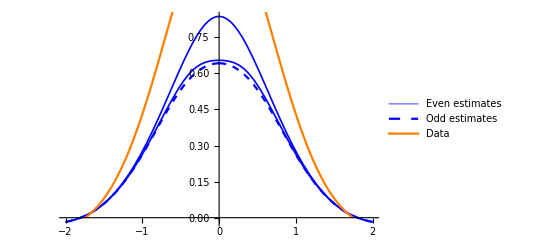

```mathematica
Show[
Plot[{FinalFunction[0], FinalFunction[1], FinalFunction[2]}, {x,-2,2}, PlotStyle->{{Thickness[0.003], Blue}, {Dashed, Blue}}, PlotLegends->{"Even estimates", "Odd estimates"}], 
ListLinePlot[Transpose[{data[[;;,1]], data[[;;,2]]}], PlotStyle->{{Orange, Thick}}, PlotRange->{{-2,2}, {0, 2}}, PlotLegends->{"Data"}]
]
```

### Test

Solving the DE to the zeroth order doesn’t mean that the peak is the right value.

```mathematica
h[x_]:=3Cos[x] + 1
```

```mathematica
D[h[x], {x,2}]-h[x]^2
```

-3 Cos[x]-(1+3 Cos[x])^2

```mathematica
g[x_]:=A Cos[x]
```

```mathematica
Series[D[g[x], {x,2}]-g[x] + (1 + 6Cos[x]), {x,0,1}]
```

(7-2 A)+O[x]^2

```mathematica
Solve[CoefficientList[%148, {x}]==0, {A}]
```

{{A→7/2}}

```mathematica
DSolve[y''[x] - y[x]+(1+6Cos[x])==0, y, x]
```

{{y→Function[{x},1+ⅇ^x C[1]+ⅇ^-x C[2]+3 Cos[x]]}}

```mathematica
f[x_]:=A Exp[σ x]
```

```mathematica
f''''[x] + 4σ^4f[x] + Γ f[x]^3
```

A^3 ⅇ^(3 x σ) Γ+5 A ⅇ^(x σ) σ^4

```mathematica
Series[%83 /. param, {x,0,2}]
```

(30 A-24 A^3)+(30 6^(1/4) A-72 6^(1/4) A^3) x+(15 √6 A-108 √6 A^3) x^2+O[x]^3

## Taylor Expansion 2

```mathematica
htrigident = {
			cosh^k_-> (1+sinh^2)^(Floor[k/2]) cosh^(Mod[k,2])
		};
		trigident = {
			Cos[x σ]^k_-> (1-Sin[x σ]^2)^(Floor[k/2]) Cos[x σ]^(Mod[k,2]) /. param
		};
```

```mathematica
f[x_]:=SubAnswers[u[0][x] + u[1][x], 2] /. param
```

```mathematica
CoefficientList[((4 σ^4f[x]+f''''[x] + Γ(u[0][x] )^3 /. {Csch[_] -> 1/sinh, Sech[_] -> 1/cosh, Coth[_] -> cosh / sinh,Tanh[_] -> sinh/cosh}) // Together //Numerator) /. htrigident /. trigident /. param, {cosh,sinh}]  // FullSimplify
```

{{0,180 (80 A+60 A^3+480 B-27 A^2 B+48 A B^2-3 B^3) Sin[6^(1/4) x] Sin[2 6^(1/4) x],0,54 ((441 A^3+3120 B-199 A^2 B-27 B^3+7 A (80+51 B^2)) Cos[6^(1/4) x]-(369 A^3+3120 B-219 A^2 B-47 B^3+3 A (80+111 B^2)) Cos[3 6^(1/4) x]),0,12 (3 (1146 A^3+6720 B-519 A^2 B-87 B^3+2 A (680+431 B^2)) Cos[6^(1/4) x]+(-2208 A^3-20640 B+1863 A^2 B+639 B^3+4 A (380-549 B^2)) Cos[3 6^(1/4) x]),0,6 (3 (1779 A^3+8080 B-831 A^2 B-123 B^3+A (3440+1183 B^2)) Cos[6^(1/4) x]-5 (525 A^3+6000 B-729 A^2 B-477 B^3+A (-2800+513 B^2)) Cos[3 6^(1/4) x]),0,360 (21 A^3+80 B-33 A^2 B-21 B^3+A (-80+B^2)) Cos[6^(1/4) x]-240 (2 A-3 B) (-80+9 A^2+9 B^2) Cos[3 6^(1/4) x],0,0},{-1080 (9 A^3+80 B-6 A^2 B+9 A B^2-2 B^3) Sin[6^(1/4) x]^3,0,36 ((160 A-789 A^3-6480 B+546 A^2 B-813 A B^2+198 B^3) Sin[6^(1/4) x]+(117 A^3+1360 B-162 A^2 B-86 B^3+3 A (-160+63 B^2)) Sin[3 6^(1/4) x]),0,-6 (15 (465 A^3-341 A^2 B+5 B (688-21 B^2)+3 A (-80+167 B^2)) Sin[6^(1/4) x]+(8880 A+603 A^3-560 B+1017 A^2 B-729 A B^2+861 B^3) Sin[3 6^(1/4) x]),0,-6 (3 (1557 A^3+9840 B-1103 A^2 B-99 B^3+3 A (-560+603 B^2)) Sin[6^(1/4) x]+5 (387 A^3+2320 B+63 A^2 B+51 B^3+15 A (112+9 B^2)) Sin[3 6^(1/4) x]),0,-360 (80 A+21 A^3+80 B+A^2 B+33 A B^2+21 B^3) Sin[6^(1/4) x]-240 (3 A+2 B) (80+9 A^2+9 B^2) Sin[3 6^(1/4) x],0,0,0}}

```mathematica
Solve[Series[4 σ^4f[x]+f''''[x] + Γ f[x]^3 == 0 /. param, {x,0,2}], {A,B}, Assumptions ->{{A,B}>0}] // N
```

{{A→0.242423,B→0.898534},{A→12.4387,B→6.26542}}

### Plot

```mathematica
data = Import["/Users/cory/Sync/USYD/Denison/MATLAB/PQS analytic/PureQuartic.csv"];
```

```mathematica
estimates = %122[[1]]
```

{A→0.242423,B→0.898534}

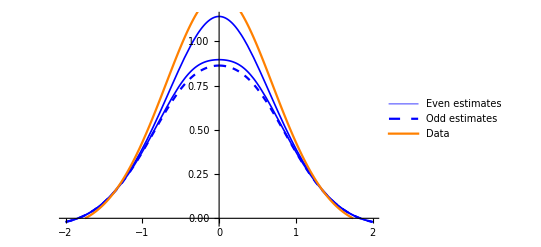

```mathematica
Show[
Plot[{FinalFunction[0], FinalFunction[1], FinalFunction[2]}, {x,-2,2}, PlotStyle->{{Thickness[0.003], Blue}, {Dashed, Blue}}, PlotLegends->{"Even estimates", "Odd estimates"}], 
ListLinePlot[Transpose[{data[[;;,1]], data[[;;,2]]}], PlotStyle->{{Orange, Thick}}, PlotRange->{{-2,2}, {0, 2}}, PlotLegends->{"Data"}]
]
```

#### Higher orders

```mathematica
f[x_]:=SubAnswers[u[0][x] + u[1][x] + u[2][x] + u[3][x], 4] /. param
```

```mathematica
NSolve[Series[4 σ^4f[x]+f''''[x] + Γ f[x]^3 == 0 /. param, {x,0,2}], {A,B},Reals]
```

General::munfl: 4.85848×10^-205 (-1.17×10^-106) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -9.76933×10^-208 (-1.31257×10^-107) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.8446×10^-210 (-1.47252×10^-108) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{A→0,B→0},{A→-9.93573,B→-6.30504×10^16},{A→-8.87635,B→-1.03079×10^11},{A→-0.334942,B→-0.69456},{A→0.334942,B→0.69456},{A→8.87635,B→1.03079×10^11},{A→9.93573,B→6.30504×10^16}}

```mathematica
A / B /. estimates
```

0.433205

```mathematica
A / B /. {A->0.33494186742400267,B->0.6945601303275414}
```

0.482236

```mathematica
A / B /.  {A->0.242423,B->0.898534}
```

0.269798